## V1: I define a generalized version of the vertices to account for the b factors. The idea would be to use: χ -> b*χ + b(b-1)/2 χ χ + ...

```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
<<bLRW`
```

D:\Offline_Documents\University\PhD_Paris\PhD_work\Simulations\MathematicaFiles-LRW-DLA\bLRW\bLRW-Diagrams

# Field Theory tools

## V[] rules

The vertices are where the interaction takes place in the field theory.

```mathematica
ClearAll[V];
V[1.]:=1.;
V[1]:=1;
V[0]:=0;
(*V'[DD[a__]]:=DD[a]/a;(*(ToExpression["δ"<>ToString[a]]);*)*)
V'[a_]:=1;
V''[a_]:=0;
V'''[a_]:=0;
```

## SpaceVertices definition

### WITH POWER COUNTING

```mathematica
ClearAll[Vγ1,Vγ1Minus,Vγ1gχ,Vγ1gχMinus,Vγ1gψ,Vγ1gψMinus,Vγ2,Vγ2Minus,Vγ2gχ,Vγ2gχMinus,Vγ2gψ,Vγ2gψMinus,Vψψ,Vψχ,Vδψχ,Vχχ,g];

Vγ1[space_,time_]:= V[γ Subscript[g, γ] ϕ[space,Subscript[t, time]]χs[space,1,2,Subscript[t, time]]ϕs[space,Subscript[t, time+1]]ψs[space,Subscript[t, time+1]]];

Vγ2[space_,time_]:= V[γ2 DD[ϕ[space,Subscript[t, time]]]χs[space,1,2,Subscript[t, time]]ϕs[space,Subscript[t, time+1]]];
Vγ2Minus[space_,time_]:= V[-γ2 ϕ[space,Subscript[t, time]]DD[χs[space,1,2,Subscript[t, time]]]ϕs[space,Subscript[t, time+1]]];

Vψχ[space_,time_]:= Module[{r},r=RandomInteger[{1,100000}];V[-g̃ ψ[space,Subscript[t, time]]χ[space,Subscript[i, r],Subscript[α, r],Subscript[t, time]]χs[space,Subscript[i, r],Subscript[α, r],Subscript[t, time]]]
];

(*Vχχ[space_,time_]:= V[-g/2 χ[space,Subscript[i, 1],Subscript[α, 1],Subscript[t, time]]χ[space,Subscript[i, 2],Subscript[α, 2],Subscript[t, time]]χs[space,Subscript[i, 1],Subscript[α, 1],Subscript[t, time]]χs[space,Subscript[i, 2],Subscript[α, 2],Subscript[t, time]]];*)
```

### Generalization for bLRW

```mathematica
ClearAll[Vγ1,Vγ1b,b];

Vγ1[space_,time_]:=Module[{r},r=RandomInteger[{1,100000}];
V[γ Subscript[g, γ] ϕ[space,Subscript[t, time]](1+b*δχs[space,1,2,Subscript[t, time]]+b(b-1)/2*δχs[space,1,Subscript[α, r],Subscript[t, time]]*δχs[space,1,Subscript[α, r],Subscript[t, time]])ϕs[space,Subscript[t, time+1]]ψs[space,Subscript[t, time+1]]];
];
```

# DIAGRAMS FOR ψ-PLUCKING OBSERVABLE, i.e. γ_1

## 1-Loop:

### OneLoop

```mathematica
nInteractionVertices=1;
nγ2=0;
nγ2Minus=0;
endTime=nInteractionVertices+nγ2+nγ2Minus+1;AbsoluteTiming[OneLoop=WickContractionSpaceVerticesMODfaster[V[ϕs[Subscript[x, 0],Subscript[t, 1]]]Spreadγ[nInteractionVertices+1,"print"->False,"nγ2"->nγ2,"nγ2Minus"->nγ2Minus]SpreadInteractions[nInteractionVertices,"endTime"->(endTime)],"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->(endTime),"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->True,"maxContractions"->100]]
```

{0.0370425,-b γ^2 g̃ g_γ^2 ϕs[x_2,t_3] χs[x_1,1,2,t_2] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_χ[x_1,x_2,t_2] G_ψ[x_1,x_1,t_2]-b^2 γ^2 g̃ g_γ^2 δχs[x_1,1,2,t_1] ϕs[x_2,t_3] χs[x_1,1,2,t_2] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_χ[x_1,x_2,t_2] G_ψ[x_1,x_1,t_2]+1/2 b^2 γ^2 g̃ g_γ^2 δχs[x_1,1,2,t_1]^2 ϕs[x_2,t_3] χs[x_1,1,2,t_2] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_χ[x_1,x_2,t_2] G_ψ[x_1,x_1,t_2]-1/2 b^3 γ^2 g̃ g_γ^2 δχs[x_1,1,2,t_1]^2 ϕs[x_2,t_3] χs[x_1,1,2,t_2] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_χ[x_1,x_2,t_2] G_ψ[x_1,x_1,t_2]}

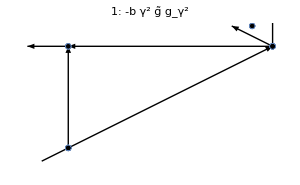

```mathematica
DrawFromContraction[OneLoop/.δχs[__]->0,"print"->False,"showEndLines"->True,"ImageSize"->300,"export"->False,"exportDirectory"->("D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\MathematicaFiles-LRW-DLA\\Diagrams\\DiagramsDrawings\\OneLoop\\"<>"OneLoop.pdf")]
```

```mathematica
(* This looks ok, let's see 2-Loop*)
```

## 2-Loop:

### TwoLoopBackbone

```mathematica
nInteractionVertices=2;
nγ2=0;
nγ2Minus=0;
endTime=nInteractionVertices+nγ2+nγ2Minus+1;

(V[ϕs[Subscript[x, 0],Subscript[t, 1]]]Spreadγ[nInteractionVertices+1,"print"->False,"nγ2"->nγ2,"nγ2Minus"->nγ2Minus,"δfields"->False]);

AbsoluteTiming[TwoLoopBackbone=WickContractionSpaceVerticesMODfaster[#,"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->(endTime),"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->False,"FreeAction"->NONE,"maxContractions"->100]&@%;]
```

{0.0528104,Null}

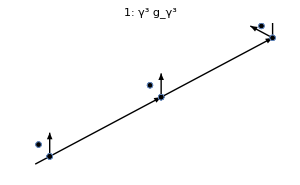
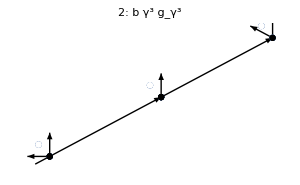
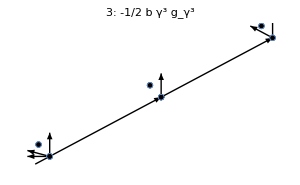
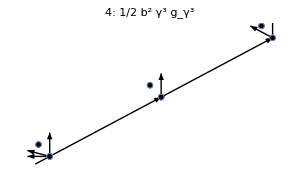
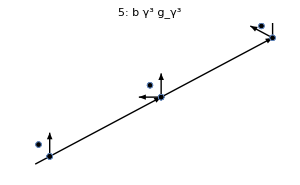
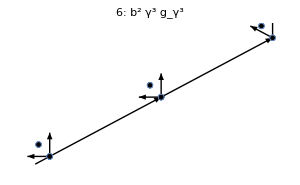
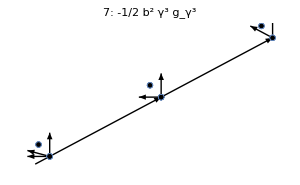
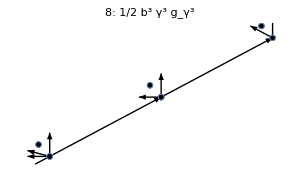

```mathematica
DrawFromContraction[TwoLoopBackbone,"print"->False,"showEndLines"->True,"ImageSize"->300]
```

#### ψχ contraction from TwoLoopBackbone

```mathematica
nInteractionVertices=2;
nγ2=0;
nγ2Minus=0;
endTime=nInteractionVertices+nγ2+nγ2Minus+1;

skele=(List@@(Plus@@(TwoLoopBackbone*(List@@SpreadInteractions[nInteractionVertices,"endTime"->endTime,"Vγ2δ"->True]))));
```

```mathematica
TwoLoopWITHbackbone={0,0,0,0,0,0};
```

```mathematica
Timing[
Table[
TwoLoopWITHbackbone[[iii]]=WickContractionSpaceVerticesMODfasterForδFields[skele[[iii]],"fields"->FieldsNamesGenerator[{ψ,χ}], "endTime"->(endTime),"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->True,"maxContractions"->nInteractionVertices];
,{iii,1,Length[skele]}]
]
```

{1084.39,{Null,Null,Null,Null,Null,Null}}

```mathematica
TwoLoopWITHbackbone[[1]]
```

2 b γ^3 (g̃)^2 g_γ^3 ϕs[x_3,t_4] χs[x_2,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_χ[x_2,x_1,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]+2 b^2 γ^3 (g̃)^2 g_γ^3 δχs[x_1,1,2,t_1] ϕs[x_3,t_4] χs[x_2,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_χ[x_2,x_1,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]-b^2 γ^3 (g̃)^2 g_γ^3 δχs[x_1,1,2,t_1]^2 ϕs[x_3,t_4] χs[x_2,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_χ[x_2,x_1,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]+b^3 γ^3 (g̃)^2 g_γ^3 δχs[x_1,1,2,t_1]^2 ϕs[x_3,t_4] χs[x_2,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_χ[x_2,x_1,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]+2 b^2 γ^3 (g̃)^2 g_γ^3 δχs[x_2,1,2,t_2] ϕs[x_3,t_4] χs[x_2,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_χ[x_2,x_1,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]+2 b^3 γ^3 (g̃)^2 g_γ^3 δχs[x_1,1,2,t_1] δχs[x_2,1,2,t_2] ϕs[x_3,t_4] χs[x_2,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_χ[x_2,x_1,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]-b^3 γ^3 (g̃)^2 g_γ^3 δχs[x_1,1,2,t_1]^2 δχs[x_2,1,2,t_2] ϕs[x_3,t_4] χs[x_2,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_χ[x_2,x_1,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]+b^4 γ^3 (g̃)^2 g_γ^3 δχs[x_1,1,2,t_1]^2 δχs[x_2,1,2,t_2] ϕs[x_3,t_4] χs[x_2,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_χ[x_2,x_1,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]-b^2 γ^3 (g̃)^2 g_γ^3 δχs[x_2,1,2,t_2]^2 ϕs[x_3,t_4] χs[x_2,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_χ[x_2,x_1,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]+b^3 γ^3 (g̃)^2 g_γ^3 δχs[x_2,1,2,t_2]^2 ϕs[x_3,t_4] χs[x_2,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_χ[x_2,x_1,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]-b^3 γ^3 (g̃)^2 g_γ^3 δχs[x_1,1,2,t_1] δχs[x_2,1,2,t_2]^2 ϕs[x_3,t_4] χs[x_2,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_χ[x_2,x_1,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]+b^4 γ^3 (g̃)^2 g_γ^3 δχs[x_1,1,2,t_1] δχs[x_2,1,2,t_2]^2 ϕs[x_3,t_4] χs[x_2,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_χ[x_2,x_1,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]+1/2 b^3 γ^3 (g̃)^2 g_γ^3 δχs[x_1,1,2,t_1]^2 δχs[x_2,1,2,t_2]^2 ϕs[x_3,t_4] χs[x_2,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_χ[x_2,x_1,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]-b^4 γ^3 (g̃)^2 g_γ^3 δχs[x_1,1,2,t_1]^2 δχs[x_2,1,2,t_2]^2 ϕs[x_3,t_4] χs[x_2,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_χ[x_2,x_1,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]+1/2 b^5 γ^3 (g̃)^2 g_γ^3 δχs[x_1,1,2,t_1]^2 δχs[x_2,1,2,t_2]^2 ϕs[x_3,t_4] χs[x_2,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_χ[x_2,x_1,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]+2 b γ^3 (g̃)^2 g_γ^3 ϕs[x_3,t_4] χs[x_1,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_2,t_3] G_χ[x_2,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]+2 b^2 γ^3 (g̃)^2 g_γ^3 δχs[x_1,1,2,t_1] ϕs[x_3,t_4] χs[x_1,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_2,t_3] G_χ[x_2,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]-b^2 γ^3 (g̃)^2 g_γ^3 δχs[x_1,1,2,t_1]^2 ϕs[x_3,t_4] χs[x_1,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_2,t_3] G_χ[x_2,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]+b^3 γ^3 (g̃)^2 g_γ^3 δχs[x_1,1,2,t_1]^2 ϕs[x_3,t_4] χs[x_1,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_2,t_3] G_χ[x_2,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]+2 b^2 γ^3 (g̃)^2 g_γ^3 δχs[x_2,1,2,t_2] ϕs[x_3,t_4] χs[x_1,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_2,t_3] G_χ[x_2,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]+2 b^3 γ^3 (g̃)^2 g_γ^3 δχs[x_1,1,2,t_1] δχs[x_2,1,2,t_2] ϕs[x_3,t_4] χs[x_1,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_2,t_3] G_χ[x_2,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]-b^3 γ^3 (g̃)^2 g_γ^3 δχs[x_1,1,2,t_1]^2 δχs[x_2,1,2,t_2] ϕs[x_3,t_4] χs[x_1,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_2,t_3] G_χ[x_2,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]+b^4 γ^3 (g̃)^2 g_γ^3 δχs[x_1,1,2,t_1]^2 δχs[x_2,1,2,t_2] ϕs[x_3,t_4] χs[x_1,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_2,t_3] G_χ[x_2,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]-b^2 γ^3 (g̃)^2 g_γ^3 δχs[x_2,1,2,t_2]^2 ϕs[x_3,t_4] χs[x_1,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_2,t_3] G_χ[x_2,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]+b^3 γ^3 (g̃)^2 g_γ^3 δχs[x_2,1,2,t_2]^2 ϕs[x_3,t_4] χs[x_1,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_2,t_3] G_χ[x_2,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]-b^3 γ^3 (g̃)^2 g_γ^3 δχs[x_1,1,2,t_1] δχs[x_2,1,2,t_2]^2 ϕs[x_3,t_4] χs[x_1,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_2,t_3] G_χ[x_2,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]+b^4 γ^3 (g̃)^2 g_γ^3 δχs[x_1,1,2,t_1] δχs[x_2,1,2,t_2]^2 ϕs[x_3,t_4] χs[x_1,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_2,t_3] G_χ[x_2,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]+1/2 b^3 γ^3 (g̃)^2 g_γ^3 δχs[x_1,1,2,t_1]^2 δχs[x_2,1,2,t_2]^2 ϕs[x_3,t_4] χs[x_1,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_2,t_3] G_χ[x_2,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]-b^4 γ^3 (g̃)^2 g_γ^3 δχs[x_1,1,2,t_1]^2 δχs[x_2,1,2,t_2]^2 ϕs[x_3,t_4] χs[x_1,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_2,t_3] G_χ[x_2,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]+1/2 b^5 γ^3 (g̃)^2 g_γ^3 δχs[x_1,1,2,t_1]^2 δχs[x_2,1,2,t_2]^2 ϕs[x_3,t_4] χs[x_1,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_2,t_3] G_χ[x_2,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]

```mathematica
TwoLoopWITHbackboneKilledχ=Plus@@Table[TwoLoopWITHbackbone[[iii]]/.δχs[__]->0,{iii,1,Length[skele]}]
```

b^2 γ^3 (g̃)^2 g_γ^3 ϕs[x_3,t_4] χs[x_1,1,2,t_2] χs[x_2,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_2,t_2] G_χ[x_2,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_2,x_2,t_3]+2 b γ^3 (g̃)^2 g_γ^3 ϕs[x_3,t_4] χs[x_2,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_χ[x_2,x_1,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]+2 b γ^3 (g̃)^2 g_γ^3 ϕs[x_3,t_4] χs[x_1,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_2,t_3] G_χ[x_2,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]

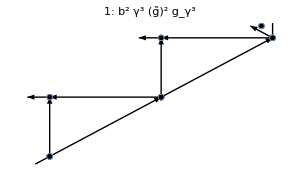
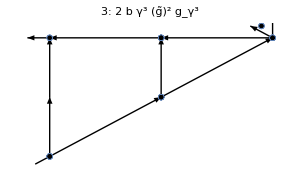
-Graphics--Graphics--Graphics-

```mathematica
DrawFromContraction[TwoLoopWITHbackboneKilledχ,"print"->False,"showEndLines"->True,"ImageSize"->300]
```

```mathematica
(*!!! NOT WORKING !!!*)
```

### TwoLoop directly fails with δχ

```mathematica
nInteractionVertices=2;
nγ2=0;
nγ2Minus=0;
endTime=nInteractionVertices+nγ2+nγ2Minus+1;

AbsoluteTiming[TwoLoop=WickContractionSpaceVerticesMODfasterForδFields[V[ϕs[Subscript[x, 0],Subscript[t, 1]]]Spreadγ[nInteractionVertices+1,"print"->False,"nγ2"->nγ2,"nγ2Minus"->nγ2Minus]SpreadInteractions[nInteractionVertices,"endTime"->(endTime)],"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->(endTime),"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->True,"maxContractions"->3]]
```

{132.883,b^2 γ^3 (g̃)^2 g_γ^3 ϕs[x_3,t_4] χs[x_1,1,2,t_2] χs[x_2,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_2,t_2] G_χ[x_2,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_2,x_2,t_3]+b^3 γ^3 (g̃)^2 g_γ^3 δχs[x_1,1,2,t_1] ϕs[x_3,t_4] χs[x_1,1,2,t_2] χs[x_2,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_2,t_2] G_χ[x_2,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_2,x_2,t_3]-1/2 b^3 γ^3 (g̃)^2 g_γ^3 δχs[x_1,1,2,t_1]^2 ϕs[x_3,t_4] χs[x_1,1,2,t_2] χs[x_2,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_2,t_2] G_χ[x_2,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_2,x_2,t_3]+1/2 b^4 γ^3 (g̃)^2 g_γ^3 δχs[x_1,1,2,t_1]^2 ϕs[x_3,t_4] χs[x_1,1,2,t_2] χs[x_2,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_2,t_2] G_χ[x_2,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_2,x_2,t_3]}

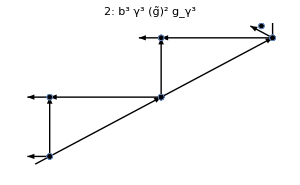
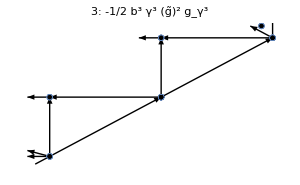
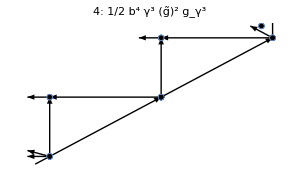
-Graphics--Graphics--Graphics--Graphics-

```mathematica
DrawFromContraction[TwoLoop,"print"->False,"showEndLines"->True,"ImageSize"->300,"export"->False,"exportDirectory"->("D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\MathematicaFiles-LRW-DLA\\Diagrams\\DiagramsDrawings\\OneLoop\\"<>"OneLoop.pdf")]
```

```mathematica
(* This looks ok, let's see 2-Loop*)
```

# DIAGRAMS FOR COUPLING RENORMALIZATION

## 1-Loop:

### OneLoopBackbone

```mathematica
nInteractionVertices=1;
nγ2=0;
nγ2Minus=0;
endTime=nInteractionVertices+nγ2+nγ2Minus+1;

(V[ϕs[Subscript[x, 0],Subscript[t, 1]]]Spreadγ[nInteractionVertices+1,"print"->False,"nγ2"->nγ2,"nγ2Minus"->nγ2Minus,"δfields"->False]V[δχs[Subscript[x, 10],1,2,Subscript[t, endTime]]])

AbsoluteTiming[OneLoopBackbone=WickContractionSpaceVerticesMODfaster[#,"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->(endTime),"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->False,"FreeAction"->NONE,"maxContractions"->100]&@%;]
```

V[δχs[x_10,1,2,t_2]] V[ϕs[x_0,t_1]] V[γ g_γ ϕ[x_1,t_1] ϕs[x_1,t_2] χs[x_1,1,2,t_1] ψs[x_1,t_2]] V[γ g_γ ϕ[x_2,t_2] ϕs[x_2,t_3] χs[x_2,1,2,t_2] ψs[x_2,t_3]]

{0.0026299,Null}

```mathematica
OneLoopBackbone
```

γ^2 g_γ^2 V[δχs[x_10,1,2,t_2]] ϕs[x_2,t_3] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] ψs[x_1,t_2] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2]

```mathematica
DrawFromContraction[OneLoopBackbone,"print"->False,"showEndLines"->True,"ImageSize"->300]
```

-Graphics-

#### ψχ contraction from TwoLoopBackbone

```mathematica
nInteractionVertices=2;
nγ2=0;
nγ2Minus=0;
endTime=nInteractionVertices+nγ2+nγ2Minus+1;

skele=(List@@(Plus@@(TwoLoopBackbone*(List@@SpreadInteractions[nInteractionVertices,"endTime"->endTime,"Vγ2δ"->True]))));
```

```mathematica
TwoLoopWITHbackbone={0,0,0,0,0,0};
```

```mathematica
Timing[
Table[
TwoLoopWITHbackbone[[iii]]=WickContractionSpaceVerticesMODfasterForδFields[skele[[iii]],"fields"->FieldsNamesGenerator[{ψ,χ}], "endTime"->(endTime),"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->True,"maxContractions"->nInteractionVertices];
,{iii,1,Length[skele]}]
]
```

{1084.39,{Null,Null,Null,Null,Null,Null}}

```mathematica
TwoLoopWITHbackbone[[1]]
```

2 b γ^3 (g̃)^2 g_γ^3 ϕs[x_3,t_4] χs[x_2,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_χ[x_2,x_1,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]+2 b^2 γ^3 (g̃)^2 g_γ^3 δχs[x_1,1,2,t_1] ϕs[x_3,t_4] χs[x_2,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_χ[x_2,x_1,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]-b^2 γ^3 (g̃)^2 g_γ^3 δχs[x_1,1,2,t_1]^2 ϕs[x_3,t_4] χs[x_2,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_χ[x_2,x_1,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]+b^3 γ^3 (g̃)^2 g_γ^3 δχs[x_1,1,2,t_1]^2 ϕs[x_3,t_4] χs[x_2,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_χ[x_2,x_1,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]+2 b^2 γ^3 (g̃)^2 g_γ^3 δχs[x_2,1,2,t_2] ϕs[x_3,t_4] χs[x_2,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_χ[x_2,x_1,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]+2 b^3 γ^3 (g̃)^2 g_γ^3 δχs[x_1,1,2,t_1] δχs[x_2,1,2,t_2] ϕs[x_3,t_4] χs[x_2,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_χ[x_2,x_1,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]-b^3 γ^3 (g̃)^2 g_γ^3 δχs[x_1,1,2,t_1]^2 δχs[x_2,1,2,t_2] ϕs[x_3,t_4] χs[x_2,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_χ[x_2,x_1,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]+b^4 γ^3 (g̃)^2 g_γ^3 δχs[x_1,1,2,t_1]^2 δχs[x_2,1,2,t_2] ϕs[x_3,t_4] χs[x_2,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_χ[x_2,x_1,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]-b^2 γ^3 (g̃)^2 g_γ^3 δχs[x_2,1,2,t_2]^2 ϕs[x_3,t_4] χs[x_2,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_χ[x_2,x_1,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]+b^3 γ^3 (g̃)^2 g_γ^3 δχs[x_2,1,2,t_2]^2 ϕs[x_3,t_4] χs[x_2,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_χ[x_2,x_1,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]-b^3 γ^3 (g̃)^2 g_γ^3 δχs[x_1,1,2,t_1] δχs[x_2,1,2,t_2]^2 ϕs[x_3,t_4] χs[x_2,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_χ[x_2,x_1,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]+b^4 γ^3 (g̃)^2 g_γ^3 δχs[x_1,1,2,t_1] δχs[x_2,1,2,t_2]^2 ϕs[x_3,t_4] χs[x_2,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_χ[x_2,x_1,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]+1/2 b^3 γ^3 (g̃)^2 g_γ^3 δχs[x_1,1,2,t_1]^2 δχs[x_2,1,2,t_2]^2 ϕs[x_3,t_4] χs[x_2,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_χ[x_2,x_1,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]-b^4 γ^3 (g̃)^2 g_γ^3 δχs[x_1,1,2,t_1]^2 δχs[x_2,1,2,t_2]^2 ϕs[x_3,t_4] χs[x_2,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_χ[x_2,x_1,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]+1/2 b^5 γ^3 (g̃)^2 g_γ^3 δχs[x_1,1,2,t_1]^2 δχs[x_2,1,2,t_2]^2 ϕs[x_3,t_4] χs[x_2,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_χ[x_2,x_1,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]+2 b γ^3 (g̃)^2 g_γ^3 ϕs[x_3,t_4] χs[x_1,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_2,t_3] G_χ[x_2,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]+2 b^2 γ^3 (g̃)^2 g_γ^3 δχs[x_1,1,2,t_1] ϕs[x_3,t_4] χs[x_1,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_2,t_3] G_χ[x_2,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]-b^2 γ^3 (g̃)^2 g_γ^3 δχs[x_1,1,2,t_1]^2 ϕs[x_3,t_4] χs[x_1,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_2,t_3] G_χ[x_2,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]+b^3 γ^3 (g̃)^2 g_γ^3 δχs[x_1,1,2,t_1]^2 ϕs[x_3,t_4] χs[x_1,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_2,t_3] G_χ[x_2,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]+2 b^2 γ^3 (g̃)^2 g_γ^3 δχs[x_2,1,2,t_2] ϕs[x_3,t_4] χs[x_1,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_2,t_3] G_χ[x_2,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]+2 b^3 γ^3 (g̃)^2 g_γ^3 δχs[x_1,1,2,t_1] δχs[x_2,1,2,t_2] ϕs[x_3,t_4] χs[x_1,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_2,t_3] G_χ[x_2,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]-b^3 γ^3 (g̃)^2 g_γ^3 δχs[x_1,1,2,t_1]^2 δχs[x_2,1,2,t_2] ϕs[x_3,t_4] χs[x_1,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_2,t_3] G_χ[x_2,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]+b^4 γ^3 (g̃)^2 g_γ^3 δχs[x_1,1,2,t_1]^2 δχs[x_2,1,2,t_2] ϕs[x_3,t_4] χs[x_1,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_2,t_3] G_χ[x_2,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]-b^2 γ^3 (g̃)^2 g_γ^3 δχs[x_2,1,2,t_2]^2 ϕs[x_3,t_4] χs[x_1,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_2,t_3] G_χ[x_2,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]+b^3 γ^3 (g̃)^2 g_γ^3 δχs[x_2,1,2,t_2]^2 ϕs[x_3,t_4] χs[x_1,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_2,t_3] G_χ[x_2,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]-b^3 γ^3 (g̃)^2 g_γ^3 δχs[x_1,1,2,t_1] δχs[x_2,1,2,t_2]^2 ϕs[x_3,t_4] χs[x_1,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_2,t_3] G_χ[x_2,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]+b^4 γ^3 (g̃)^2 g_γ^3 δχs[x_1,1,2,t_1] δχs[x_2,1,2,t_2]^2 ϕs[x_3,t_4] χs[x_1,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_2,t_3] G_χ[x_2,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]+1/2 b^3 γ^3 (g̃)^2 g_γ^3 δχs[x_1,1,2,t_1]^2 δχs[x_2,1,2,t_2]^2 ϕs[x_3,t_4] χs[x_1,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_2,t_3] G_χ[x_2,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]-b^4 γ^3 (g̃)^2 g_γ^3 δχs[x_1,1,2,t_1]^2 δχs[x_2,1,2,t_2]^2 ϕs[x_3,t_4] χs[x_1,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_2,t_3] G_χ[x_2,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]+1/2 b^5 γ^3 (g̃)^2 g_γ^3 δχs[x_1,1,2,t_1]^2 δχs[x_2,1,2,t_2]^2 ϕs[x_3,t_4] χs[x_1,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_2,t_3] G_χ[x_2,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]

```mathematica
TwoLoopWITHbackboneKilledχ=Plus@@Table[TwoLoopWITHbackbone[[iii]]/.δχs[__]->0,{iii,1,Length[skele]}]
```

b^2 γ^3 (g̃)^2 g_γ^3 ϕs[x_3,t_4] χs[x_1,1,2,t_2] χs[x_2,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_2,t_2] G_χ[x_2,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_2,x_2,t_3]+2 b γ^3 (g̃)^2 g_γ^3 ϕs[x_3,t_4] χs[x_2,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_χ[x_2,x_1,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]+2 b γ^3 (g̃)^2 g_γ^3 ϕs[x_3,t_4] χs[x_1,1,2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_2,t_3] G_χ[x_2,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]

```mathematica
DrawFromContraction[TwoLoopWITHbackboneKilledχ,"print"->False,"showEndLines"->True,"ImageSize"->300]
```

-Graphics--Graphics--Graphics-

```mathematica
(*!!! NOT WORKING !!!*)
```

### OneLoop

```mathematica
nInteractionVertices=1;
nγ2=0;
nγ2Minus=0;
endTime=nInteractionVertices+nγ2+nγ2Minus+1;

AbsoluteTiming[OneLoop=WickContractionSpaceVerticesMODfaster[V[ϕs[Subscript[x, 0],Subscript[t, 1]]]Spreadγ[nInteractionVertices+1,"print"->False,"nγ2"->nγ2,"nγ2Minus"->nγ2Minus]SpreadInteractions[nInteractionVertices,"endTime"->(endTime)],"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->(endTime),"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->True,"maxContractions"->100]]
```

{0.0370425,-b γ^2 g̃ g_γ^2 ϕs[x_2,t_3] χs[x_1,1,2,t_2] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_χ[x_1,x_2,t_2] G_ψ[x_1,x_1,t_2]-b^2 γ^2 g̃ g_γ^2 δχs[x_1,1,2,t_1] ϕs[x_2,t_3] χs[x_1,1,2,t_2] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_χ[x_1,x_2,t_2] G_ψ[x_1,x_1,t_2]+1/2 b^2 γ^2 g̃ g_γ^2 δχs[x_1,1,2,t_1]^2 ϕs[x_2,t_3] χs[x_1,1,2,t_2] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_χ[x_1,x_2,t_2] G_ψ[x_1,x_1,t_2]-1/2 b^3 γ^2 g̃ g_γ^2 δχs[x_1,1,2,t_1]^2 ϕs[x_2,t_3] χs[x_1,1,2,t_2] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_χ[x_1,x_2,t_2] G_ψ[x_1,x_1,t_2]}

```mathematica
DrawFromContraction[OneLoop/.δχs[__]->0,"print"->False,"showEndLines"->True,"ImageSize"->300,"export"->False,"exportDirectory"->("D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\MathematicaFiles-LRW-DLA\\Diagrams\\DiagramsDrawings\\OneLoop\\"<>"OneLoop.pdf")]
```

-Graphics-

```mathematica
(* This looks ok, let's see 2-Loop*)
```